```mathematica
(*SetDirectory["/home/schlenk/Mathematica/compact_downconversion"];*)
(*Refractive index of air*)
nair=1.000276;
(*Wavelength of pump beam in μm*)
(*λp=0.4025;*)
temp = 20
SetOptions[Plot,Frame->True,PlotStyle->{Red,Green,Blue,Black}];
SetOptions[ListPlot,Frame->True,PlotStyle->{Red,Green,Blue,Black}];
```

20

## Definitions ...

```mathematica
(* refractive index in uniaxial chrystals *)
nth[no_,ne_,θ_]:=no*ne/Sqrt[ne^2*Cos[θ]^2+no^2*Sin[θ]^2]
```

```mathematica
(* unit vector *)
vect[Θ_,ϕ_]:={Sin[Θ]*Cos[ϕ],Sin[Θ]*Sin[ϕ],Cos[Θ]};
```

```mathematica
kvect[λ_,nbr_,s__]:=2*π*nbr/λ*Normalize[s];
kvect[λ_,nbr_,Θ_,ϕ_]:=kvect[λ,nbr,vect[Θ,ϕ]];
```

```mathematica
(* Length of a crystal at Temperature T, L0 at 20°C *)
LT[L0_,α_,T_]:= L0+L0*(T-20)*α;
(* YVO4: α= 11.3 , see YVO4_temperature_12082015.nb *)
(* BBO: αa = 4*10^-6/K, αc=36*10^-6/K, Foctek homepage *)
```

## Sellmeier Equations

### YVO4

```mathematica
(*Sellmeier equations of Yttrium Vanadate crystals, Handbook of nonlinear optical crystals *)
(* http://www.redoptronics.com/Nd-YVO4-crystal.html 
http://www.foctek.net/products/YVO4.htm
thermal expansion: aa=4.43x10-6/K,ac=11.37x10-6/K
*)
nYVO[lambda_,temp_,axis:(e|o)]:=Module[{nr,x},
nr=If[MatchQ[axis,o],
Sqrt[(3.77834+0.069736/(lambda^2-0.04724)-0.0108133*lambda^2)]*(1+(temp-20)*8.5*10^-6),
Sqrt[4.59905+0.110534/(lambda^2-0.04813)-0.0122676*lambda^2]*(1+(temp-20)*3.0*10^-6)];
Return[nr]];
nYVO[lambda_,axis:(e|o)]:=nYVO[lambda,temp,axis];
(*Refractive index of the extraordinary wave as a function of the polar angle (α) between optic axis and k vector*)
nYVOth[λ_,temp_,α_]:=nth[nYVO[λ,temp,o],nYVO[λ,temp,e],α];
nYVOth[λ_,α_]:=nYVOth[λ,temp,α];
```

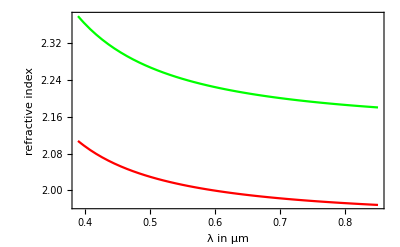

```mathematica
Plot[{nYVO[lam,20,o],nYVO[lam,20,e]},{lam,.39,.85},FrameLabel->{"λ in μm","refractive index"}]
```

### BBO

```mathematica
(*Sellmeier equations of BBO crystals *)
nBBO[lambda_,temp_,axis:(e|o)]:=Module[{nq,x},
nq=If[MatchQ[axis,o],
2.7359+0.01878/(lambda^2-0.01822)-0.01354*lambda^2,
2.3753+0.01224/(lambda^2-0.01667)-0.01516*lambda^2];
Sqrt[nq]+(InterpolatingPolynomial[If[MatchQ[axis,o],{{1.014,-16.64},{.579,-16.35},{.4047,-16.83}},{{1.014,-9.76},{.5790,-9.42},{.4047,-8.84}}],x]//.x->lambda)*10^-6*(temp-20)]
nBBO[lambda_,axis:(e|o)]:=nBBO[lambda,20,axis];
(*Refractive index of the extraordinary wave as a function of the polar angle (α) between optic axis and k vector*)
nBBOth[λ_,temp_,θ_]:=nth[nBBO[λ,temp,o],nBBO[λ,temp,e],θ];
nBBOth[λ_,θ_]:=nBBOth[λ,temp,θ];
```

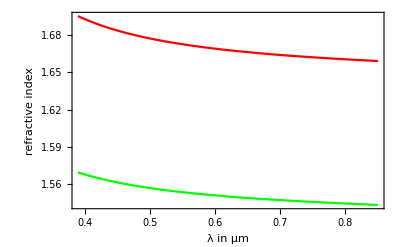

```mathematica
Plot[{nBBO[lam,20,o],nBBO[lam,20,e]},{lam,.39,.85},FrameLabel->{"λ in μm","refractive index"}]
```

## phases state is |HH> + Exp[Iϕ] |VV>. ϕ is a function of λp, λs and λi only relative phases are important

### phases in the two down conversion BBO crystals

-Graphics-

the relative phase between HH and VV is calculated:
   |HH> + Exp[I*ϕ] |VV>

assumption: HH are generated in first BBO crystal,

BBOs:
first BBO crystal: H:ordinary, V:extraordinary
second BBO crystal: V:ordinary, H:extraordinary
difference of phases:
HH: extra-ordinary in second crystal
VV: pump beam ordinary in first crystal
exp(i*(kse+kie)L)|HH> + exp(i*kpo*L) |VV>
same quantum state: |HH> + exp(i*(kpo-kse-kie))*L ) |VV> 

pre-comp:
V(pump): ordinary

comp:
H(signal) and H(idler) ordinary

!!! pre-comp and comp optical axis in the same direction

```mathematica
Δdc = (kpo-(kse+kie))L
```

(-kie+kpo-kse) L

### phase in pre-compensation crystal

relative phase, 
H: ordinary ,V: extraordinary
exp(i*kpeYVO*Lpc)|HH> + exp(i*kpoYVO*Lpc)*exp(i*Δdc ) |VV>

```mathematica
Δpc = (kpoYVO-kpeYVO4)*Lpc
```

(-kpeYVO4+kpoYVO) Lpc

### phase in compensation crystal

relative phase, 
H: ordinary ,V: extraordinary
exp(i*(ksoYVO+kioYVO)*Lc)|HH> + exp(i*(kseYVO+kieYVO)*Lc)*exp(i*(Δdc+Δpc ) |VV>

```mathematica
Δc = (kseYVO+kieYVO-(ksoYVO+kioYVO))*Lc
```

(kieYVO-kioYVO+kseYVO-ksoYVO) Lc

|HH> + exp(i*(Δdc+Δpc +Δc)) |VV>

### phase behind all crystals, dc crystal and compensation with different length and material

```mathematica
Δpc + Δdc + Δc
```

(-kie+kpo-kse) L+(kieYVO-kioYVO+kseYVO-ksoYVO) Lc+(-kpeYVO4+kpoYVO) Lpc

```mathematica
pckvect = {kpeYVO4-> 2*π*nYVO[λp,Tpc,e]/λp,kpoYVO-> 2*π*nYVO[λp,Tpc,o]/λp};
ckvect =  {ksoYVO->2*π*nYVO[λs,Tc,o]/λs,kseYVO->2*π*nYVO[λs,Tc,e]/λs,kioYVO->2*π*nYVO[λi,Tc,o]/λi,kieYVO->2*π*nYVO[λi,Tc,e]/λi};
dckvect ={kpo-> 2*π*nBBO[λp,TBBO,o]/λp,kse->2*π*nBBOth[λs,TBBO,θp]/λs,kie->2*π*nBBOth[λi,TBBO,θp]/λi};
```

```mathematica
ϕdc[θp_,λp_,λs_,λi_,L_,Lc_,Lpc_,TBBO_,Tc_,Tpc_]:=Evaluate[(Δpc +Δdc + Δc/. pckvect /.dckvect /.ckvect)];
ϕdc[θp_,λp_,λs_,L_,Lc_,Lpc_,TBBO_,Tc_,Tpc_]:=ϕdc[θp,λp,λs,(1/λp-1/λs)^(-1),L,Lc,Lpc,TBBO,Tc,Tpc]
```

## phase compensation calculations

{L→6000.,Lc→3120.,Lpc→0.,TBBO→20,Tc→20,Tpc→20}

{λp→0.406,λs→0.765,Tbbo→20,ϕp→π/2,θp→0.502658}

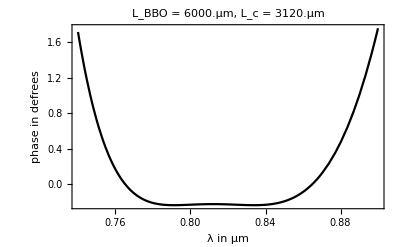

```mathematica
sourceparameters = {L-> 6000.,Lc-> 3120.,Lpc->0.,TBBO->20,Tc->20,Tpc->20}
DCParameters = {λp->0.406,λs->.765,Tbbo->20,ϕp->π/2,θp->0.5026584054092709}
Plot[180/π(ϕdc[θp,λp,λS,L,Lc,Lpc,TBBO,Tc,Tpc]-ϕdc[θp,λp,λs,L,Lc,Lpc,TBBO,Tc,Tpc])/.sourceparameters/.DCParameters,{λS,.740,.9},FrameLabel->{ "λ in µm","phase in defrees"},ImageSize->400,PlotRange->All,PlotLabel->"L_BBO = "<>ToString[L/.sourceparameters]<>"µm, L_c = "<>ToString[Lc/.sourceparameters]<>"µm"]
```

```mathematica
ϕdc[θp,λp,λs+.01,L,Lc,Lpc,TBBO,Tc,Tpc]-ϕdc[θp,λp,λs,L,Lc,Lpc,TBBO,Tc,Tpc]/.sourceparameters/.DCParameters 
%*180/π
```

-0.00309556

-0.177362

{L→6000.,Lc→2870.,Lpc→0.,TBBO→20,Tc→20,Tpc→20}

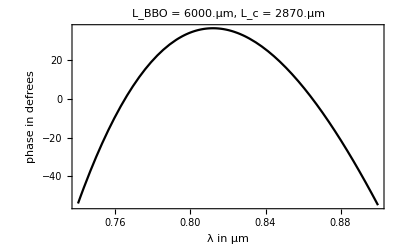

```mathematica
sourceparameters = {L-> 6000.,Lc-> 3120.-250,Lpc->0.,TBBO->20,Tc->20,Tpc->20}
DCParameters = {λp->0.406,λs->.765,Tbbo->20,ϕp->π/2,θp->0.5026584054092709};Plot[180/π(ϕdc[θp,λp,λS,L,Lc,Lpc,TBBO,Tc,Tpc]-ϕdc[θp,λp,λs,L,Lc,Lpc,TBBO,Tc,Tpc])/.sourceparameters/.DCParameters,{λS,.740,.9},FrameLabel->{ "λ in µm","phase in defrees"},ImageSize->400,PlotRange->All,PlotLabel->"L_BBO = "<>ToString[L/.sourceparameters]<>"µm, L_c = "<>ToString[Lc/.sourceparameters]<>"µm"]
```

{L→6000.,Lc→3370.,Lpc→0.,TBBO→20,Tc→20,Tpc→20}

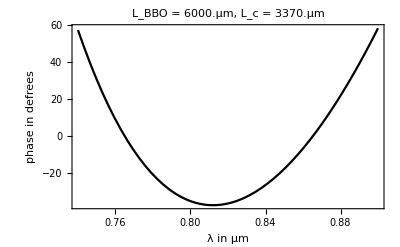

```mathematica
sourceparameters = {L-> 6000.,Lc-> 3120.+250.,Lpc->0.,TBBO->20,Tc->20,Tpc->20}
DCParameters = {λp->0.406,λs->.765,Tbbo->20,ϕp->π/2,θp->0.5026584054092709};Plot[180/π(ϕdc[θp,λp,λS,L,Lc,Lpc,TBBO,Tc,Tpc]-ϕdc[θp,λp,λs,L,Lc,Lpc,TBBO,Tc,Tpc])/.sourceparameters/.DCParameters,{λS,.740,.9},FrameLabel->{ "λ in µm","phase in defrees"},ImageSize->400,PlotRange->All,PlotLabel->"L_BBO = "<>ToString[L/.sourceparameters]<>"µm, L_c = "<>ToString[Lc/.sourceparameters]<>"µm"]
```